```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
xTicks={{0,"θ_a"},{3,"θ_b"}};
```

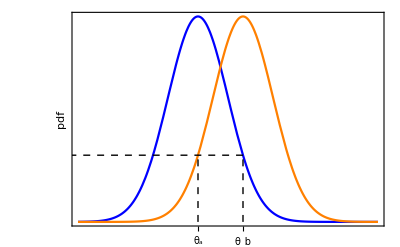

```mathematica
gFinal=Plot[{PDF[NormalDistribution[0,2],x],PDF[NormalDistribution[3,2],x]},{x,-8,12},PlotRange->Full,PlotStyle->{Blue,Orange},Frame->{True,True,False,False},Axes->{True,False},FrameTicks->{xTicks,None},Epilog->{{Dashed,Line[{{0,0},{0,PDF[NormalDistribution[3,2],0]}}]},{Dashed,Line[{{3,0},{3,PDF[NormalDistribution[0,2],3]}}]},{Dashed,Line[{{3,PDF[NormalDistribution[0,2],3]},{-10,PDF[NormalDistribution[0,2],3]}}]}},FrameLabel->{"","pdf"},BaseStyle->Medium]
```

```mathematica
Export["metropolisHastings_normalProposal.pdf",gFinal]
```

metropolisHastings_normalProposal.pdf